# SpinDynamica Optimal Control Tutorial 02: Two-Spin Transfers, Ensembles, Relaxation, and Time-Optimal Control

## Heteronuclear transfers, cooperative and trajectory-penalized objectives, robust broadband/B1 ensembles, Liouville relaxation, quantum speed limit searches, and Pontryagin diagnostics.

## 0. Setup and Loading SpinDynamica

Evaluate both setup cells in order. Cell 1 locates the SpinDynamica repository root upward from NotebookDirectory[] using System` symbols only and loads SpinDynamica`; Cell 2 verifies that all OptimalControl` packages (including Ensemble, TimeOptimal, and Visualization) loaded cleanly.

```mathematica
nbRepoRoot=Quiet[Check[NotebookDirectory[],Directory[]]];
While[StringQ[nbRepoRoot]&&nbRepoRoot=!=""&&!FileExistsQ[FileNameJoin[{nbRepoRoot,"SpinDynamica","SpinDynamica.m"}]],With[{parent=ParentDirectory[nbRepoRoot]},If[parent===nbRepoRoot,nbRepoRoot=Directory[];Break[],nbRepoRoot=parent]]];
If[FileExistsQ[FileNameJoin[{nbRepoRoot,"SpinDynamica","SpinDynamica.m"}]],Needs["SpinDynamica`",FileNameJoin[{nbRepoRoot,"SpinDynamica","SpinDynamica.m"}]],Needs["SpinDynamica`"]];
```

SetUserLevel::ini: The user level is being initialized to 2. The user level may be set to an integer between 1 and 3 by using SetUserLevel[level]. Low user levels provide strong syntax trapping at the expense of slow execution for some routines. High user levels relax the syntax trapping in order to provide better execution speeds.

SetUserLevel::ul: The user level has been set to 2.

SetUserLevel::modsymbs: Additional definitions have been given to the following symbols: {Commutator, Duration, Exp, Expand, Plus, Power, Simplify, SolidAngle, Times, WignerD}

```mathematica
{Select[$Packages,StringStartsQ[#,"OptimalControl`"]&],Context[OptimalControlEnsemble],Context[TimeOptimalControlOptimize]}
```

{{OptimalControl`Visualization`,OptimalControl`TimeOptimal`,OptimalControl`SecondOrderOptimizers`,OptimalControl`Optimizers`,OptimalControl`Ensemble`,OptimalControl`GRAPE`,OptimalControl`Objectives`,OptimalControl`Kernels`},OptimalControl`Ensemble`,OptimalControl`TimeOptimal`}

## 1. Two-Spin Polarization and Coherence Transfer

In a coupled heteronuclear {1H, 15N} two-spin-1/2 liquid-state system (nuH = +120 Hz, nuN = -160 Hz, J_HN = 92 Hz), we provide four RF control channels: {1H x, 1H y, 15N x, 15N y} bounded on each RF channel pair by AmplitudeNormBound -> {{1, 2} -> 1000., {3, 4} -> 1000.} Hz.

Notice the physics of ObservableTarget vs CoherenceTarget:
  - ObservableTarget[Iz^H -> Iz^N] transfers longitudinal magnetization via J-coupling (requires duration ~ 1.2/J_HN for full transfer).
  - CoherenceTarget[I-^H -> I-^N] handles non-Hermitian raising/lowering spin coherences, with PhaseInsensitive -> False (exact phase) or True (arbitrary receiver phase).

```mathematica
SetSpinSystem[{{"1H",1/2},{"15N",1/2}}];
nuH=120.;
nuN=-160.;
jHN=92.;
Hhn=2.*Pi*(nuH*opI["1H","z"]+nuN*opI["15N","z"]+jHN*(opI["1H","z"].opI["15N","z"]));
ctrlsHN={opI["1H","x"],opI["1H","y"],opI["15N","x"],opI["15N","y"]};
rfLimits={{1,2}->1000.,{3,4}->1000.};
resPol=GRAPEOptimize[Hhn,ctrlsHN,ObservableTarget[opI["1H","z"]->opI["15N","z"]],{1.2/jHN,40},ControlUnits->"Hz",AmplitudeNormBound->rfLimits,RandomSeed->42,TargetFidelity->0.9999];
resCohPS=GRAPEOptimize[Hhn,ctrlsHN,CoherenceTarget[opI["1H","-"]->opI["15N","-"],PhaseInsensitive->False],{1.6/jHN,48},ControlUnits->"Hz",AmplitudeNormBound->rfLimits,RandomSeed->42,TargetFidelity->0.9999];
resCohPI=GRAPEOptimize[Hhn,ctrlsHN,CoherenceTarget[opI["1H","-"]->opI["15N","-"],PhaseInsensitive->True],{1.6/jHN,48},ControlUnits->"Hz",AmplitudeNormBound->rfLimits,RandomSeed->42,TargetFidelity->0.9999];
{"Iz^H -> Iz^N Fidelity"->resPol["FinalFidelity"],"I-^H -> I-^N (PhaseSensitive)"->resCohPS["FinalFidelity"],"I-^H -> I-^N (PhaseInsensitive)"->resCohPI["FinalFidelity"],"Native SpinDynamica Check"->VerifyOptimalControlSimulation[resPol]["FidelityMatchQ"]}
```

1         1
SetSpinSystem::set : the spin system has been set to {{1H, -}, {15N, -}}
                                                           2         2

1         1
SetBasis::set : the state basis has been set to ZeemanBasis[{{1H, -}, {15N, -}}, BasisLabels -> Automatic].
                                                                  2         2

{Iz^H -> Iz^N Fidelity→0.999971,I-^H -> I-^N (PhaseSensitive)→0.999907,I-^H -> I-^N (PhaseInsensitive)→0.999909,Native SpinDynamica Check→True}

```mathematica
GraphicsRow[{PlotOptimalControlWaveform[resPol,PlotLegends->Placed[{"1Hx","1Hy","15Nx","15Ny"},Above],PlotLabel->"1H -> 15N Transfer Controls (4 ch)"],PlotOptimalControlTrajectory[resPol,opI["1H","z"],{opI["1H","z"],2.*(opI["1H","z"].opI["15N","z"]),opI["15N","z"]},PlotLegends->Placed[{"<Iz^H>","<2 Iz^H Iz^N>","<Iz^N>"},Above],PlotLabel->"INEPT-like State Trajectory"]},ImageSize->760,Spacings->25]
```

-Graphics-

What to observe: The trajectory plot reveals how the optimized pulse automatically passes through two-spin longitudinal order 2 Iz^H Iz^N near mid-pulse before arriving at pure Iz^N at the end.

## 2. Cooperative Objectives and Intermediate Trajectory Penalties

CooperativeObjective combines multiple simultaneous spin transformations into one pulse â.80.94 for example, swapping 1H -> 15N and 15N -> 1H simultaneously (NormalizeWeights -> True). RunningCost with StatePenalty penalizes (or rewards) intermediate spin states along the pulse trajectory; for example, penalizing transverse 15N coherence along the Iz^H -> Iz^N transfer. (For unitary gates confined to an embedded manifold, SubspaceUnitaryTarget with LeakageWeight plays a complementary role.)

```mathematica
resSwap=GRAPEOptimize[Hhn,ctrlsHN,CooperativeObjective[{ObservableTarget[opI["1H","z"]->opI["15N","z"]],ObservableTarget[opI["15N","z"]->opI["1H","z"]]},NormalizeWeights->True],{1.5/jHN,48},ControlUnits->"Hz",AmplitudeNormBound->rfLimits,RandomSeed->42,TargetFidelity->0.999];
resWithPenalty=GRAPEOptimize[Hhn,ctrlsHN,ObservableTarget[opI["1H","z"]->opI["15N","z"]],{1.2/jHN,40},ControlUnits->"Hz",AmplitudeNormBound->rfLimits,RunningCost->StatePenalty[opI["15N","x"],0.3,TargetMode->"Magnitude",TimeWeighting->"Uniform"],RandomSeed->42];
{"Cooperative Swap Fidelity"->resSwap["FinalFidelity"],"Unpenalized Iz^H -> Iz^N Fidelity"->resPol["FinalFidelity"],"Penalized Iz^H -> Iz^N (Fidelity, RunningCost)"->{resWithPenalty["FinalFidelity"],resWithPenalty["RunningCost"]}}
```

{Cooperative Swap Fidelity→0.999338,Unpenalized Iz^H -> Iz^N Fidelity→0.999971,Penalized Iz^H -> Iz^N (Fidelity, RunningCost)→{0.999917,-0.00199954}}

## 3. Robust Broadband and RF-Inhomogeneity Ensembles

Real NMR samples experience chemical-shift offsets and spatial RF (B1) inhomogeneity. OptimalControlEnsemble optimizes a single waveform across a parameter grid specified by EnsembleParameters (symbolic Hamiltonian parameters) and RFInhomogeneity (multiplicative scaling applied to all control channels). Here we switch back to a fast single spin-1/2 so the 1D and 2D ensemble optimizations run in under a second.

```mathematica
SetSpinSystem[{{1,1/2}}];
Clear[delta];
Hens=2.*Pi*delta*opI[1,"z"];
ens1D=OptimalControlEnsemble[Hens,{opI[1,"x"],opI[1,"y"]},ObservableTarget[opI[1,"z"]->-opI[1,"z"]],{0.002,40},EnsembleParameters->{delta->Subdivide[-800.,800.,8]},ControlUnits->"Hz",AmplitudeNormBound->1200.];
resEns1D=GRAPEOptimize[ens1D,RandomSeed->42,MaxIterations->120];
ev1D=EvaluateEnsembleFidelity[resEns1D];
KeyTake[ev1D,{"MeanFidelity","MinFidelity","MaxFidelity"}]
```

1
SetSpinSystem::set : the spin system has been set to {{1, -}}
                                                          2

1
SetBasis::set : the state basis has been set to ZeemanBasis[{{1, -}}, BasisLabels -> Automatic].
                                                                 2

<|MeanFidelity→0.998392,MinFidelity→0.996989,MaxFidelity→0.999785|>

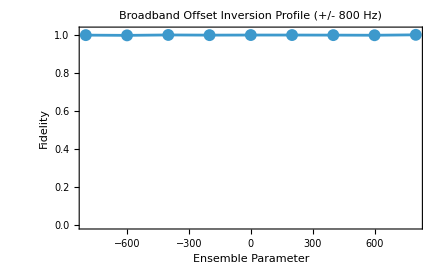

```mathematica
PlotEnsembleFidelity[resEns1D,PlotLabel->"Broadband Offset Inversion Profile (+/- 800 Hz)",ImageSize->440]
```

## 4. Mean vs Worst-Case (SoftMin) Ensemble Aggregation

Optimizing the average fidelity (EnsembleAggregation -> "Mean") can leave corner members of a 2D (offset x B1) grid significantly lower than the center. Setting EnsembleAggregation -> {"SoftMin", beta} smoothly emphasizes the worst-performing members, and SoftMinSchedule -> {0., 5., 15.} continues smoothly from Mean (beta = 0) into progressively stronger worst-case optimization.

```mathematica
ens2D=OptimalControlEnsemble[Hens,{opI[1,"x"],opI[1,"y"]},ObservableTarget[opI[1,"z"]->-opI[1,"z"]],{0.002,40},EnsembleParameters->{delta->Subdivide[-1200.,1200.,4]},RFInhomogeneity->{0.75,1.0,1.25},ControlUnits->"Hz",AmplitudeNormBound->800.];
resEnsMean=GRAPEOptimize[ens2D,EnsembleAggregation->"Mean",RandomSeed->42,MaxIterations->80];
resEnsSoftMin=GRAPEOptimize[ens2D,EnsembleAggregation->{"SoftMin",15.},SoftMinSchedule->{0.,10.},RandomSeed->42,MaxIterations->80];
{"Mean-Aggregated (Mean, Min)"->Values[KeyTake[EvaluateEnsembleFidelity[resEnsMean],{"MeanFidelity","MinFidelity"}]],"SoftMin-Aggregated (Mean, Min)"->Values[KeyTake[EvaluateEnsembleFidelity[resEnsSoftMin],{"MeanFidelity","MinFidelity"}]]}
```

{Mean-Aggregated (Mean, Min)→{0.939184,0.664954},SoftMin-Aggregated (Mean, Min)→{0.923647,0.785907}}

```mathematica
GraphicsRow[{PlotEnsembleFidelity[resEnsMean,PlotLabel->"2D Fidelity Map (Mean)"],PlotEnsembleFidelity[resEnsSoftMin,PlotLabel->"2D Fidelity Map (SoftMin Schedule)"]},ImageSize->760,Spacings->20]
```

-Graphics-

## 5. Relaxation and Liouville-Space Optimal Control

For unitary Hamiltonians, GRAPEOptimize defaults to Hilbert space. When relaxation or non-unitary damping is present, pass a Liouvillian superoperator (here CommutationSuperoperator[-I H0] + PhenomenologicalRelaxationSuperoperator[T1, T2]), specify Basis and OperatorBasis, and set PropagateSpace -> "Liouville". Below we compare unitary inversion against a dissipative system with rapid relaxation (T1 = 15 ms, T2 = 3 ms over a 2 ms pulse).

```mathematica
zb=ZeemanBasis[];
ob=ZeemanKetBraOperatorBasis[];
Hrel=2.*Pi*150.*opI[1,"z"];
Lrel=CommutationSuperoperator[-I*Hrel]+PhenomenologicalRelaxationSuperoperator[0.015,0.003];
resUnitary=GRAPEOptimize[Hrel,{opI[1,"x"],opI[1,"y"]},ObservableTarget[opI[1,"z"]->-opI[1,"z"]],{0.002,40},ControlUnits->"Hz",AmplitudeNormBound->800.,RandomSeed->42];
resLiouvRelax=GRAPEOptimize[Lrel,{opI[1,"x"],opI[1,"y"]},ObservableTarget[opI[1,"z"]->-opI[1,"z"]],{0.002,40},PropagateSpace->"Liouville",Basis->zb,OperatorBasis->ob,ControlUnits->"Hz",AmplitudeNormBound->800.,RandomSeed->42];
{"Hilbert Unitary (Space, Fidelity)"->{resUnitary["Space"],resUnitary["FinalFidelity"]},"Liouville Dissipative (Space, Fidelity)"->{resLiouvRelax["Space"],resLiouvRelax["FinalFidelity"]}}
```

{Hilbert Unitary (Space, Fidelity)→{Hilbert,0.999993},Liouville Dissipative (Space, Fidelity)→{Liouville,0.80507}}

```mathematica
GraphicsRow[{PlotOptimalControlWaveform[resUnitary,Method->"AmplitudePhase",PlotLabel->"Unitary (Hilbert)"],PlotOptimalControlWaveform[resLiouvRelax,Method->"AmplitudePhase",PlotLabel->"Relaxation T2 = 3 ms (Liouville)"]},ImageSize->760,Spacings->20]
```

-Graphics-

What to observe: Under relaxation, the optimizer cannot reach 100% inversion over 2 ms and shapes a shorter/faster-acting amplitude profile to outrun transverse T2 decay.

## 6. Time-Optimal Control and Quantum Speed Limits

Under a fixed RF ceiling (AmplitudeNormBound -> 500 Hz, whose on-resonance pi-pulse duration is 1/(2 * 500 Hz) = 1.0 ms), what is the shortest duration at which a pulse still reaches TargetFidelity -> 0.999?

SpinDynamica provides two complementary tools:
  - TimeOptimalControlOptimize: brackets and refines ShortestFeasibleDuration (Method -> "Progressive", "Joint", or "Hybrid"; FidelityCriterion; DiscretizationStrategy; WaveformRescaling; AttemptsPerDuration; optional ValidationEnsemble).
  - TimeOptimalPulseCurve + PlotTimeOptimalPulseCurve: sweeps a grid of durations to map the trade-off curve.
In addition, GRAPEOptimize itself accepts OptimizeDurations -> "Total" with DurationBounds and DurationPenalty to shrink pulse duration directly in one solve.

```mathematica
probTO=OptimalControlProblem[Hrel,{opI[1,"x"],opI[1,"y"]},ObservableTarget[opI[1,"z"]->-opI[1,"z"]],{0.0016,24},ControlUnits->"Hz",AmplitudeNormBound->500.];
toRes=TimeOptimalControlOptimize[probTO,Method->"Progressive",TargetFidelity->0.999,InitialDuration->0.0016,MinimumDuration->0.0005,DurationReductionFactor->0.75,AttemptsPerDuration->{1,2},RandomSeed->42];
curveRes=TimeOptimalPulseCurve[probTO,Subdivide[0.0007,0.0015,4],TargetFidelity->0.999,AttemptsPerDuration->{1,1},RandomSeed->42];
resJointDur=GRAPEOptimize[probTO,OptimizeDurations->"Total",DurationBounds->{0.0006,0.0025},DurationPenalty->0.05,RandomSeed->42];
{"TimeOptimal ShortestFeasibleDuration (ms)"->1000.*toRes["ShortestFeasibleDuration"],"TimeOptimal AchievedFidelity"->toRes["AchievedFidelity"],"Joint Duration Opt (ms, Fidelity)"->{1000.*resJointDur["TotalDuration"],resJointDur["FinalFidelity"]}}
```

{TimeOptimal ShortestFeasibleDuration (ms)→0.989062,TimeOptimal AchievedFidelity→0.999004,Joint Duration Opt (ms, Fidelity)→{0.996897,0.999951}}

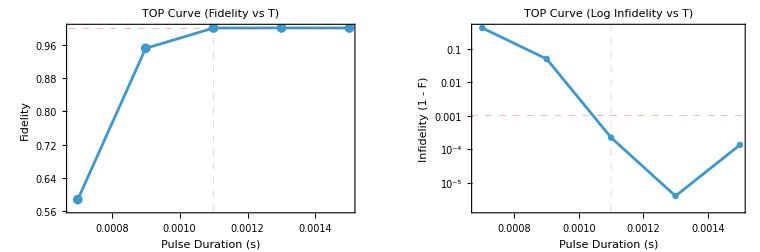

```mathematica
GraphicsRow[{PlotTimeOptimalPulseCurve[curveRes,Method->"Fidelity",PlotLabel->"TOP Curve (Fidelity vs T)"],PlotTimeOptimalPulseCurve[curveRes,Method->"Infidelity",PlotLabel->"TOP Curve (Log Infidelity vs T)"]},ImageSize->760,Spacings->20]
```

## 7. Pontryagin Stationarity Diagnostics (VerifyOptimalControlStationarity)

After polishing the time-optimal pulse down to tight gradient tolerance, VerifyOptimalControlStationarity evaluates continuous-time Pontryagin Maximum Principle (PMP) switching functions s_k(t) on sub-slice grids and measures discrete and integrated stationarity residuals. Note carefully: small switching residuals confirm local first-order constrained stationarity (necessary, not sufficient, for global or time optimality). PlotSwitchingFunctions displays the control amplitudes alongside s_k(t) and pointwise residuals.

```mathematica
resTOPolished=GRAPEOptimize[Hrel,{opI[1,"x"],opI[1,"y"]},ObservableTarget[opI[1,"z"]->-opI[1,"z"]],{toRes["ShortestFeasibleDuration"],24},ControlUnits->"Hz",AmplitudeNormBound->500.,InitialControls->toRes["BestResult"],TargetFidelity->None,GradientTolerance->10^-7,MaxIterations->200];
statRes=VerifyOptimalControlStationarity[resTOPolished,StationaritySubdivisions->8];
KeyTake[statRes,{"ApplicableQ","ConstraintType","RelativeDiscreteResidual","RelativeIntegratedResidual","StationaritySatisfiedQ"}]
```

<|ApplicableQ→True,ConstraintType→Disk,RelativeDiscreteResidual→9.77168×10^-9,RelativeIntegratedResidual→0.0000621435,StationaritySatisfiedQ→True|>

Notice also two clean diagnostic nuances: PlotSwitchingFunctions renders three stacked panels (controls, switching functions, and pointwise residual; in the current GraphicsColumn layout, the top two Legended panels may visually crop frame edges on export, while the underlying TimeGrid, ControlTimeSeries, and SwitchingFunctions arrays remain directly accessible in statRes).

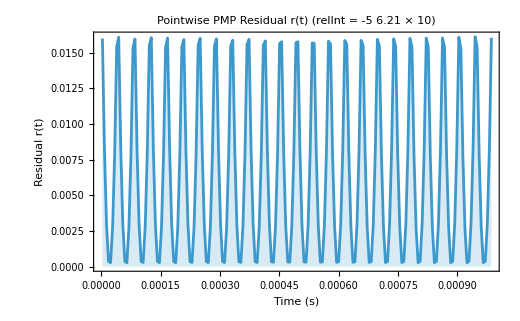

```mathematica
PlotSwitchingFunctions[statRes,ImageSize->520]
```

## 8. Summary and Quick Reference

Moving to multi-spin and realistic experimental pulse design:
  1. Use CoherenceTarget or CooperativeObjective for coupled heteronuclear transfers and multi-task pulses, optionally shaping intermediate states with RunningCost -> StatePenalty[...].
  2. Build robust pulses over offset and B1 spreads with OptimalControlEnsemble, using SoftMinSchedule when edge fidelity matters.
  3. Switch to PropagateSpace -> "Liouville" with a relaxation superoperator to quantify and compensate T1/T2 losses.
  4. Probe quantum speed limits with TimeOptimalControlOptimize / TimeOptimalPulseCurve and inspect first-order PMP optimality with VerifyOptimalControlStationarity.

Symbol / Option | Purpose | Key Notes
ObservableTarget / CoherenceTarget | Multi-spin & coherence transfers | Supports non-Hermitian operators & PhaseInsensitive -> True/False
CooperativeObjective | Weighted multi-objective sum | NormalizeWeights -> True / False
RunningCost / StatePenalty | Intermediate-time trajectory cost | TargetMode, TimeWeighting, Sign; SubspaceUnitaryTarget noted
OptimalControlEnsemble | Broadband / B1-robust ensemble | EnsembleParameters & RFInhomogeneity grids
EnsembleAggregation / SoftMinSchedule | Mean vs worst-case robustness | "Mean" or {"SoftMin", beta}; continuation schedule
EvaluateEnsembleFidelity / PlotEnsembleFidelity | Member fidelity stats & maps | Reports Mean, Min, Max; plots 1D slices or 2D maps
PropagateSpace -> "Liouville" | Open-system / relaxation GRAPE | Requires superoperator generator, Basis, OperatorBasis
TimeOptimalControlOptimize | Shortest feasible pulse duration | "Progressive", "Joint", "Hybrid"; FidelityCriterion, ValidationEnsemble
TimeOptimalPulseCurve / PlotTimeOptimalPulseCurve | Duration sweep trade-off curve | DiscretizationStrategy, WaveformRescaling, AttemptsPerDuration
OptimizeDurations / DurationBounds / Penalty | Joint duration optimization | Available directly in OptimalControlProblem / GRAPEOptimize
VerifyOptimalControlStationarity / PlotSwitchingFunctions | Continuous-time PMP stationarity check | Sub-slice s_k(t) & residuals (StationaritySubdivisions)